```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
(* Needs["CollierLink`"]*)
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../models/DipoleDM2/DipoleDM2_minimalH_FA/DipoleDM2_minimalH_FA",
ExcludeParticles->{S[1],V[1],V[2],V[3],V[4],U[1],U[2],U[3],U[4],U[5],F[14]},InsertionLevel-> {Particles},GenericModel->"../models/DipoleDM2/DipoleDM2_minimalH_FA/DipoleDM2_minimalH_FA_FC"
];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
tops = CreateTopologies[1,1->3,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT = { F[14]} -> { F[13],F[12],-F[12]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},
ExcludeParticles->{V[1],V[2],V[3],V[4],U[1],U[2],U[3],U[4],U[5],F[14],S[3],S[2],S[4]},
ExcludeFieldPoints-> {FieldPoint[_][F[14],S[4],-F[13]],FieldPoint[_][F[14],S[1],-F[13]],FieldPoint[_][S[4],S[1],S[1]],FieldPoint[_][S[4],S[4],S[1]],FieldPoint[_][S[1],S[1],S[1]],FieldPoint[_][S[4],S[4],S[4]],FieldPoint[_][F[14],S[1],S[1],-F[13]]}];
```

generic model {../models/DipoleDM2/DipoleDM2_minimalH_FA/DipoleDM2_minimalH_FA_FC} initialized

classes model {../models/DipoleDM2/DipoleDM2_minimalH_FA/DipoleDM2_minimalH_FA} initialized

in total: 2 Particles insertions

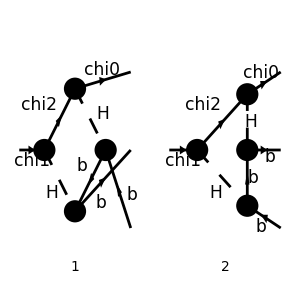

```mathematica
(* goodDiags=DiagramExtract[allDiags,{2,3}];*)
goodDiags=allDiags;
Paint[allDiags,ColumnsXRows->{2,1},ImageSize->{ 300,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False,GaugeRules->{GaugeXi[S[_]]->1}]/.{SUNT->FASUNT},IncomingMomenta->{p},LorentzIndexNames->{μ,ν},OutgoingMomenta->{k1,k2,k3},LoopMomenta->{q},SUNIndexNames->{cc3,cc4,aa,bb},SUNFIndexNames->{a,b,c2,c1},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[DiracSimplify[SUNSimplify[DiracSimplify[ampA]]]]
```

in total: 2 Particles amplitudes

1/4 sina^2 (sina^2-1) yb^2 ychi1x3 ychi2x3 δ_c1c2 (M2 (φ(k1,M0)).(φ(p,M1))+(φ(k1,M0)).(γ·q).(φ(p,M1))) (((φ(k2,MB)).(γ·k1-γ·q).(φ(-k3,MB))+2 MB (φ(k2,MB)).(φ(-k3,MB)))/((q^2-M2^2).((k1-q)^2-MH^2).((k1+k2-q)^2-MB^2).((k1+k2+k3-q)^2-MH^2))+(2 MB (φ(k2,MB)).(φ(-k3,MB))-(φ(k2,MB)).(γ·k1-γ·q).(φ(-k3,MB)))/((q^2-M2^2).((k1-q)^2-MH^2).((k1+k3-q)^2-MB^2).((k1+k2+k3-q)^2-MH^2)))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify);
```

```mathematica
ampEsimp=ExpandScalarProduct[DiracSimplify[ampC/.{DiracGamma[7]->1-DiracGamma[6]}]];
```

## On - Shell Case

since we are only interested in q q -> tt or gg -> tt, the t - t - g - g vertex only contributes when all external particles are on - shell, so we make use of this to simplify the final expressions

```mathematica
FCClearScalarProducts[];
SetMandelstam[k23,k13,k12,p,-k1,-k2,-k3,M1,M0,0,0];
```

```mathematica
ampEsimp2=ChangeDimension[Simplify[DiracSimplify[ampEsimp]/.{k12->M1^2+M0^2-k23-k13,MB->0}],4];
```

## Check Divergences

```mathematica
lInts = Cases2[ampEsimp2,{A0,B0,C0,D0,PaVe}];
tab=Table[{lInts[[i]],PaXEvaluateUV[lInts[[i]]]},{i,1,Length[lInts]}]
```

(D_1(k13,M0^2,k23,0,0,M1^2,0,M2^2,MH^2,MH^2) | 0
D_1(M0^2,M1^2,0,0,k23,-k13-k23+M0^2+M1^2,MH^2,M2^2,MH^2,0) | 0
D_00(0,0,M0^2,M1^2,k23,k13,MH^2,0,MH^2,M2^2) | 0
D_00(0,0,M0^2,M1^2,k23,-k13-k23+M0^2+M1^2,MH^2,0,MH^2,M2^2) | 0
D_11(k13,M0^2,k23,0,0,M1^2,0,M2^2,MH^2,MH^2) | 0
D_11(M0^2,M1^2,0,0,k23,-k13-k23+M0^2+M1^2,MH^2,M2^2,MH^2,0) | 0
D_12(0,k13,M0^2,k23,M1^2,0,MH^2,0,M2^2,MH^2) | 0
D_12(0,M1^2,M0^2,0,k13,k23,0,MH^2,M2^2,MH^2) | 0
D_12(0,M1^2,M0^2,0,-k13-k23+M0^2+M1^2,k23,0,MH^2,M2^2,MH^2) | 0
D_12(0,-k13-k23+M0^2+M1^2,M0^2,k23,M1^2,0,MH^2,0,M2^2,MH^2) | 0)

```mathematica
loopInts = tab[[All,1]];
loopProds=KroneckerProduct[loopInts,loopInts];
```

```mathematica
ampEsimp2
```

1/4 ⅈ π^2 sina^2 (sina^2-1) yb^2 ychi1x3 ychi2x3 δ_c1c2 (-D_00(0,0,M0^2,M1^2,k23,-k13-k23+M0^2+M1^2,MH^2,0,MH^2,M2^2) (φ(OverBar[k2])).(γ̄)^($AL($235)).(φ(-OverBar[k3])) (φ(OverBar[k1],M0)).(γ̄)^($AL($235)).(φ(p̄,M1))+D_00(0,0,M0^2,M1^2,k23,k13,MH^2,0,MH^2,M2^2) (φ(OverBar[k2])).(γ̄)^($AL($239)).(φ(-OverBar[k3])) (φ(OverBar[k1],M0)).(γ̄)^($AL($239)).(φ(p̄,M1))+(φ(OverBar[k1],M0)).(φ(p̄,M1)) (φ(OverBar[k2])).(γ̄·OverBar[k1]).(φ(-OverBar[k3])) ((M0+M2) D_1(k13,M0^2,k23,0,0,M1^2,0,M2^2,MH^2,MH^2)-(M0+M2) D_1(M0^2,M1^2,0,0,k23,-k13-k23+M0^2+M1^2,MH^2,M2^2,MH^2,0)+M0 (D_11(k13,M0^2,k23,0,0,M1^2,0,M2^2,MH^2,MH^2)-D_11(M0^2,M1^2,0,0,k23,-k13-k23+M0^2+M1^2,MH^2,M2^2,MH^2,0)))-(φ(OverBar[k2])).(γ̄·OverBar[k1]).(φ(-OverBar[k3])) D_12(0,k13,M0^2,k23,M1^2,0,MH^2,0,M2^2,MH^2) (φ(OverBar[k1],M0)).(γ̄·OverBar[k3]).(φ(p̄,M1))-(φ(OverBar[k2])).(γ̄·OverBar[k1]).(φ(-OverBar[k3])) D_12(0,M1^2,M0^2,0,k13,k23,0,MH^2,M2^2,MH^2) (φ(OverBar[k1],M0)).(γ̄·OverBar[k2]+γ̄·OverBar[k3]).(φ(p̄,M1))+(φ(OverBar[k2])).(γ̄·OverBar[k1]).(φ(-OverBar[k3])) D_12(0,M1^2,M0^2,0,-k13-k23+M0^2+M1^2,k23,0,MH^2,M2^2,MH^2) (φ(OverBar[k1],M0)).(γ̄·OverBar[k2]+γ̄·OverBar[k3]).(φ(p̄,M1))+(φ(OverBar[k2])).(γ̄·OverBar[k1]).(φ(-OverBar[k3])) D_12(0,-k13-k23+M0^2+M1^2,M0^2,k23,M1^2,0,MH^2,0,M2^2,MH^2) (φ(OverBar[k1],M0)).(γ̄·OverBar[k2]).(φ(p̄,M1)))

## Amplitude Squared

```mathematica
ampSquared= FermionSpinSum[(ampEsimp2 (ComplexConjugate[ampEsimp2])),ExtraFactor->1/2]/.{SUNFDelta[SUNFIndex[c1],SUNFIndex[c2]]->1}//DiracSimplify//Simplify;
```

### Coefficients for each product of loop functions

```mathematica
coeffs=Table[{i,j,Simplify[Coefficient[Expand[ampSquared/(Pi^4 sina^4(sina^2-1)^2 yb^4 ychi1x3^2 ychi2x3^2)],loopInts[[i]]loopInts[[j]]]]},{i,1,Length[loopInts]},{j,i,Length[loopInts]}];
```

#### Check that the coefficients reproduce the full result

```mathematica
ampSquaredFromCoeffs = (Pi^4 sina^4(sina^2-1)^2 yb^4 ychi1x3^2 ychi2x3^2)Total[Table[Total[Table[loopInts[[coeffs[[i,j]][[1]]]] loopInts[[coeffs[[i,j]][[2]]]]coeffs[[i,j]][[3]],{j,1,Length[coeffs[[i]]]}]],{i,1,Length[coeffs]}]];
```

```mathematica
FullSimplify[ampSquaredFromCoeffs-ampSquared]
```

0

## Evaluate differential decay rate for a point in phase space

```mathematica
Needs["CollierLink`"]
```

CollierLink v1.0.1, by Hiren H. Patel
For more information, see the

```mathematica
dGFunc[k13v_?NumericQ,k23v_?NumericQ,M0v_?NumericQ,M1v_?NumericQ,M2v_?NumericQ,MHv_?NumericQ]:=Module[{k12v,reps,loopIntsNum,coeffsNum,amp2Num,dG},
k23min = 0;
k23max=(M1v-M0v)^2;
k13min=1/2(M1v^2 + M0v^2 -k23v - √((M1v^2+M0v^2-k23v)^2-4 M1v^2 M0v^2));
k13max=1/2(M1v^2 + M0v^2 -k23v + √((M1v^2+M0v^2-k23v)^2-4 M1v^2 M0v^2));
If[!Between[k23v,{k23min,k23max}]|| !Between[k13v,{k13min,k13max}],Return[0.0]];
k12v=M1v^2+M0v^2-k23v-k13v;
Print["input=",k13v,",  ",k23v, ", " ,k12v];
reps={M0->M0v,M1->M1v,M2->M2v,MH->MHv,k23->k23v,k13->k13v,k12->k12v};
loopIntsNum =Table[PaXEvaluate[ loopInts[[i]]/.reps],{i,1,Length[loopInts]}];
Print["loops=",loopIntsNum];
coeffsNum=coeffs/.reps;
Print["coeffs=",coeffsNum];
amp2Num=Total[Table[Total[Table[loopIntsNum[[coeffsNum[[i,j]][[1]]]] loopIntsNum[[coeffsNum[[i,j]][[2]]]]coeffsNum[[i,j]][[3]],{j,1,Length[coeffsNum[[i]]]}]],{i,1,Length[coeffsNum]}]];
 1/(256 Pi^3)1/M1v^3 amp2Num
(*Return[dG];*)
]
```

```mathematica
m0=100.;
m1=400.;
m2=407.;
mh=125.;
x13min:=1/2(m1^2 + m0^2 -x23 - √((m1^2+m0^2-x23)^2-4 m1^2 m0^2));
x13max:=1/2(m1^2 + m0^2 -x23 + √((m1^2+m0^2-x23)^2-4 m1^2 m0^2));
x23min=0;
x23max=(m1-m0)^2;
NIntegrate[dGFunc[x13,x23,m0,m1,m2,mh],{x23,x23min,x23max},{x13,x13min,x13max},Method->{Automatic,"SymbolicProcessing"->0}]
```

input=40000.,  90000., 40000.

loops={-5.96459×10^-11-2.73496×10^-11 ⅈ,-5.96459×10^-11-2.73496×10^-11 ⅈ,-5.30037×10^-6-1.50455×10^-6 ⅈ,-5.30037×10^-6-1.50455×10^-6 ⅈ,9.73573×10^-12+1.2762×10^-12 ⅈ,9.73573×10^-12+1.2762×10^-12 ⅈ,1.72397×10^-11+3.24188×10^-12 ⅈ,1.91034×10^-11+1.24792×10^-11 ⅈ,1.91034×10^-11+1.24792×10^-11 ⅈ,1.72397×10^-11+3.24188×10^-12 ⅈ}

coeffs={(1 | 1 | 0.
1 | 2 | 0.
1 | 3 | 0.
1 | 4 | 0.
1 | 5 | 0.
1 | 6 | 0.
1 | 7 | 0.
1 | 8 | 0.
1 | 9 | 0.
1 | 10 | 0.),(2 | 2 | 0.
2 | 3 | 0.
2 | 4 | 0.
2 | 5 | 0.
2 | 6 | 0.
2 | 7 | 0.
2 | 8 | 0.
2 | 9 | 0.
2 | 10 | 0.),(3 | 3 | 0.
3 | 4 | 0.
3 | 5 | 0.
3 | 6 | 0.
3 | 7 | 0.
3 | 8 | 0.
3 | 9 | 0.
3 | 10 | 0.),(4 | 4 | 0.
4 | 5 | 0.
4 | 6 | 0.
4 | 7 | 0.
4 | 8 | 0.
4 | 9 | 0.
4 | 10 | 0.),(5 | 5 | 0.
5 | 6 | 0.
5 | 7 | 0.
5 | 8 | 0.
5 | 9 | 0.
5 | 10 | 0.),(6 | 6 | 0.
6 | 7 | 0.
6 | 8 | 0.
6 | 9 | 0.
6 | 10 | 0.),(7 | 7 | 0.
7 | 8 | 0.
7 | 9 | 0.
7 | 10 | 0.),(8 | 8 | 0.
8 | 9 | 0.
8 | 10 | 0.),(9 | 9 | 0.
9 | 10 | 0.),(10 | 10 | 0.)}

input=x13,  x23, -x13-x23+170000.

LoopRefine::inexact: Unable to convert Passarino-Veltman function PVD(0,1,0,0,10000.,160000.,0,0,x23,x13,125.,407.,125.,0) with inexact or complex arguments.

PaXEvaluate::gen: PaXEvaluate has encountered an error and must abort the evaluation. The error description reads: Failed to eliminate EpsilonBar.

$Aborted

```mathematica
x13max
```

1/2 (√((170000.-x23)^2-6.4×10^9)-x23+170000.)

```mathematica
{x23,0,(M1v-M0v)^2}
{x13,x13min,x13max}
```

{x23,0,90000.}

{x13,1/2 (-√((170000.-x23)^2-6.4×10^9)-x23+170000.),1/2 (√((170000.-x23)^2-6.4×10^9)-x23+170000.)}

```mathematica
dGFunc[((x13max+x13min)/2)/.{x23->(x23max+x23min)/2},(x23max+x23min)/2,M0v,M1v,M2v,MHv]
```

2.33444×10^-16+1.02517×10^-29 ⅈ